```mathematica
First we define the Hamiltonian - Classical and Quantum
```

-and Classical Quantum+define First Hamiltonian the we

```mathematica
H = ω1  n1[t]+ω2 n2[t] +ω3 n3[t] + 2g12 Sqrt[n1[t]n2[t]]Cos[ϕ1[t]-ϕ2[t]]+2g13 Sqrt[n1[t] n3[t]]Cos[ϕ1[t]-ϕ3[t]]+2g23 Sqrt[n2[t] n3[t]]Cos[ϕ2[t]-ϕ3[t]];
Hq=({{ω1, g12, g13}, {g12, ω2, g23}, {g13, g23, ω3}});
```

Next, we define the equation of motion for the classical Hamiltionian and specifiy parameters and initial conditions

```mathematica
diffs={D[n1[t],t]==D[H,ϕ1[t]],D[n2[t],t]==D[H,ϕ2[t]],D[n3[t],t]==D[H,ϕ3[t]],D[ϕ1[t],t]==-D[H,n1[t]],D[ϕ2[t],t]==-D[H,n2[t]],D[ϕ3[t],t]==-D[H,n3[t]]};
initials1={n1[0]==0.2,n2[0]==0.3,n3[0]==0.5,ϕ1[0]==0,ϕ2[0]==0,ϕ3[0]==0};
initials2={n1[0]==0.23250621727114146,n2[0]==0.7500780197363931,n3[0]==0.0174157629924655,ϕ1[0]==0.0,ϕ2[0]==0,ϕ3[0]==0.0};
subs ={g12->Sqrt[2],g13->Sqrt[3],g23->1, ω1->1, ω2->2,ω3->0};
```

We define the function that governs the differential equation for the energy envelope and solve the corresponding equation

```mathematica
f[N1_,N2_,subs_]:=Module[{Hb=((H/.{ϕ1[t]->0,ϕ2[t]->0,ϕ3[t]->0,n1[t]->n1,n2[t]->n2,n3[t]->1-n1-n2})/.subs)},dn1=D[Hb, n1]/.{n1->N1, n2->N2};dn2=D[Hb,n2]/.{n1->N1, n2->N2};
a= dn2/Sqrt[dn1*dn1+dn2*dn2];
b= -dn1/Sqrt[dn1*dn1+dn2*dn2];
{a,b}];
resEnergyEnvelope=NDSolve[{x'[t]==f[x[t],y[t],subs][[1]],y'[t]==f[x[t],y[t],subs][[2]],x[0]==.2,y[0]==.3},{x,y},{t,0,3}];
```

```mathematica
resTrajectory1=NDSolve[Join[diffs,initials1]/.subs, {D[n1[t],t],D[n2[t],t],D[n3[t],t],n1[t],n2[t],n3[t],ϕ1[t],ϕ2[t],ϕ3[t]},{t,0,200}];
resTrajectory2=NDSolve[Join[diffs,(initials2/.{t0->0})]/.subs, {D[n1[t],t],D[n2[t],t],D[n3[t],t],n1[t],n2[t],n3[t],ϕ1[t],ϕ2[t],ϕ3[t]},{t,0,200}];
```

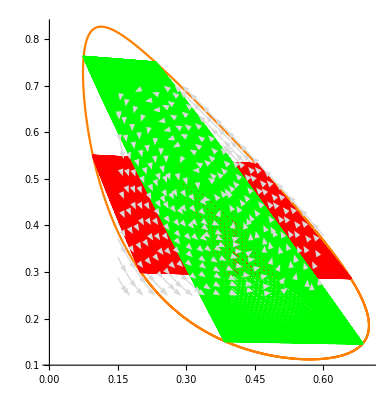

```mathematica
plotEnergyEnvelope=ParametricPlot[{(x/.resEnergyEnvelope[[1]])[t],(y/.resEnergyEnvelope[[1]])[t]},{t,0,3},PlotStyle->Orange];
plotEnergyEnvelopeStreams=StreamPlot[f[x,y,subs],{x,.15,.6},{y,.25,.7},StreamStyle->LightGray];
plotTrayectory1 = ParametricPlot[{n1[t],n2[t]}/.resTrajectory1[[1]],{t,0,80},PlotStyle->Red];
plotTrayectory2 = ParametricPlot[{n1[t],n2[t]}/.resTrajectory2[[1]],{t,0,80},PlotStyle->Green];
Show[plotEnergyEnvelope,plotEnergyEnvelopeStreams,plotTrayectory1,plotTrayectory2]
```

```mathematica
eigS=N[Eigensystem[Hq/.subs]];
λ1 = eigS[[1,1]];
λ2 = eigS[[1,2]];
λ3 = eigS[[1,3]];
e1 = eigS[[2,1]];
e2 = eigS[[2,2]];
e3 = eigS[[2,3]];
fnc[t_,ϵ1_,init_]:={( init[[1]] e1 Exp[ⅈ (λ1+ϵ1) t]+ init[[2]]e2 Exp[ⅈ (λ2) t]+ init[[3]] e3 Exp[ⅈ λ3 t])*( init[[1]] e1 Exp[-ⅈ (λ1+ϵ1) t]+ init[[2]] e2 Exp[-ⅈ (λ2) t]+ init[[3]] e3 Exp[-ⅈ λ3 t])};
det[xx_,yy_,init_]:=Det[({{D[fnc[x,y,init][[1,1]],x], D[fnc[x,y,init][[1,2]],x]}, {D[fnc[x,y,init][[1,1]],y], D[fnc[x,y,init][[1,2]],y]}})/.{x->xx,y->yy}];
a1=(Inverse[Transpose[eigS[[2]]]].Sqrt[initials1[[1;;3,2]]]);
a2=(Inverse[Transpose[eigS[[2]]]].Sqrt[initials2[[1;;3,2]]]);

env[N1_,N2_, inits_]:=N[Module[{initials=inits, fnc,determinante, dn1,dn2,x,y},
fnc[t_,ϵ1_]:={( initials[[1]] e1 Exp[ⅈ (λ1+ϵ1) t]+ initials[[2]]e2 Exp[ⅈ (λ2) t]+ initials[[3]] e3 Exp[ⅈ λ3 t])*( initials[[1]] e1 Exp[-ⅈ (λ1+ϵ1) t]+ initials[[2]] e2 Exp[-ⅈ (λ2) t]+ initials[[3]] e3 Exp[-ⅈ λ3 t])};
determinante[xx_,yy_]:=Det[({{D[fnc[x,y][[1,1]],x], D[fnc[x,y][[1,2]],x]}, {D[fnc[x,y][[1,1]],y], D[fnc[x,y][[1,2]],y]}})/.{x->xx,y->yy}];
dn1=D[determinante[x,y], x]/.{x->N1,y->N2};
dn2=D[determinante[x,y], y]/.{x->N1,y->N2};
a= dn2/Sqrt[dn1*dn1+dn2*dn2];
b= -dn1/Sqrt[dn1*dn1+dn2*dn2];
{Chop[a],Chop[b]}]];
```

```mathematica
root=FindRoot[Re[det[t,0,a1]],{t,0.6}];
res3=NDSolve[{x'[t]==env[x[t],y[t],a1][[1]],y'[t]==env[x[t],y[t],a1][[2]],x[0]==(t/.root),y[0]==0},{x,y},{t,-30,30}];
p6=ParametricPlot[fnc[x[t]/.res3[[1]],y[t]/.res3[[1]],a1][[1,1;;2]],{t,-30,30}];
p6i3D=ParametricPlot3D[1.005*Sqrt[fnc[x[t]/.res3[[1]],y[t]/.res3[[1]],a1][[1]]],{t,-30,30}];
root=FindRoot[Re[det[t,0,a1]],{t,0.9}];
res3=NDSolve[{x'[t]==env[x[t],y[t],a1][[1]],y'[t]==env[x[t],y[t],a1][[2]],x[0]==(t/.root),y[0]==0},{x,y},{t,-30,30}];
p7=ParametricPlot[fnc[x[t]/.res3[[1]],y[t]/.res3[[1]],a1][[1,1;;2]],{t,-30,30}];
p7i3D=ParametricPlot3D[1.005*Sqrt[fnc[x[t]/.res3[[1]],y[t]/.res3[[1]],a1][[1]]],{t,-30,30}];
root=FindRoot[Re[det[t,0,a1]],{t,1.2}];
res3=NDSolve[{x'[t]==env[x[t],y[t],a1][[1]],y'[t]==env[x[t],y[t],a1][[2]],x[0]==(t/.root),y[0]==0},{x,y},{t,-20,20}];
p8=ParametricPlot[fnc[x[t]/.res3[[1]],y[t]/.res3[[1]],a1][[1,1;;2]],{t,-20,20}];
p8i3D=ParametricPlot3D[1.005*Sqrt[fnc[x[t]/.res3[[1]],y[t]/.res3[[1]],a1][[1]]],{t,-20,20}];
root=FindRoot[Re[det[t,0,a1]],{t,41.5}];
res3=NDSolve[{x'[t]==env[x[t],y[t],a1][[1]],y'[t]==env[x[t],y[t],a1][[2]],x[0]==(t/.root),y[0]==0},{x,y},{t,-20,20}];
p9=ParametricPlot[fnc[x[t]/.res3[[1]],y[t]/.res3[[1]],a1][[1,1;;2]],{t,-20,20}];
p9i3D=ParametricPlot3D[1.005*Sqrt[fnc[x[t]/.res3[[1]],y[t]/.res3[[1]],a1][[1]]],{t,-20,20}];
plotEnvelopeTrajectory1 = {p6,p7,p8,p9};
plotEnvelopeTrajectory1i3D = {p6i3D,p7i3D,p8i3D,p9i3D};
```

```mathematica
root=FindRoot[Re[det[t,0,a2]],{t,0.6}];
res3=NDSolve[{x'[t]==env[x[t],y[t],a2][[1]],y'[t]==env[x[t],y[t],a2][[2]],x[0]==(t/.root),y[0]==0},{x,y},{t,-30,30}];
p10=ParametricPlot[fnc[x[t]/.res3[[1]],y[t]/.res3[[1]],a2][[1,1;;2]],{t,-30,30}];
p10i3D=ParametricPlot3D[1.005Sqrt[fnc[x[t]/.res3[[1]],y[t]/.res3[[1]],a2][[1]]],{t,-30,30}];
root=FindRoot[Re[det[t,0,a2]],{t,0.9}];
res3=NDSolve[{x'[t]==env[x[t],y[t],a1][[1]],y'[t]==env[x[t],y[t],a2][[2]],x[0]==(t/.root),y[0]==0},{x,y},{t,-30,30}];
p11=ParametricPlot[fnc[x[t]/.res3[[1]],y[t]/.res3[[1]],a2][[1,1;;2]],{t,-30,30}];
p11i3D=ParametricPlot3D[1.005Sqrt[fnc[x[t]/.res3[[1]],y[t]/.res3[[1]],a2][[1]]],{t,-30,30}];
root=FindRoot[Re[det[t,0,a2]],{t,1.2}];
res3=NDSolve[{x'[t]==env[x[t],y[t],a2][[1]],y'[t]==env[x[t],y[t],a2][[2]],x[0]==(t/.root),y[0]==0},{x,y},{t,-20,20}];
p12=ParametricPlot[fnc[x[t]/.res3[[1]],y[t]/.res3[[1]],a2][[1,1;;2]],{t,-20,20}];
p12i3D=ParametricPlot3D[1.005Sqrt[fnc[x[t]/.res3[[1]],y[t]/.res3[[1]],a2][[1]]],{t,-20,20}];
root=FindRoot[Re[det[t,0,a2]],{t,41.5}];
res3=NDSolve[{x'[t]==env[x[t],y[t],a2][[1]],y'[t]==env[x[t],y[t],a2][[2]],x[0]==(t/.root),y[0]==0},{x,y},{t,-20,20}];
p13=ParametricPlot[fnc[x[t]/.res3[[1]],y[t]/.res3[[1]],a2][[1,1;;2]],{t,-20,20}];
p13i3D=ParametricPlot3D[1.005Sqrt[fnc[x[t]/.res3[[1]],y[t]/.res3[[1]],a2][[1]]],{t,-20,20}];
plotEnvelopeTrajectory2 = {p10,p13,p12};
plotEnvelopeTrajectory2i3D = {p10i3D,p13i3D,p12i3D};
```

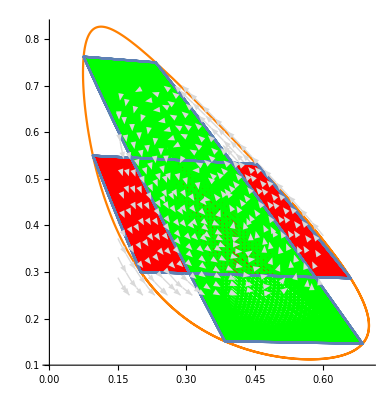

```mathematica
Show[plotEnergyEnvelope,plotEnergyEnvelopeStreams,plotTrayectory1,plotTrayectory2,plotEnvelopeTrajectory1,plotEnvelopeTrajectory2]
```

```mathematica
surface=SphericalPlot3D[1,{θ,0,Pi/2},{ϕ,0, Pi/2}, PlotStyle->Directive[LightBlue,Opacity[0.6]], Mesh->None, BoundaryStyle->Gray,ViewPoint->{5,2.5,1},BoxRatios->{1,1,1}, TicksStyle->Directive[FontOpacity->0,FontSize->0], ImageSize->300];
```

```mathematica
plotEnergyEnvelope3D=ParametricPlot3D[{Sqrt[(x/.resEnergyEnvelope[[1]])[t]],Sqrt[(y/.resEnergyEnvelope[[1]])[t]],Sqrt[(1-(x/.resEnergyEnvelope[[1]])[t]-(y/.resEnergyEnvelope[[1]])[t])]},{t,0,3},PlotStyle->Orange];
plotTrayectory1i3D = ParametricPlot3D[{Sqrt[n1[t]],Sqrt[n2[t]],Sqrt[n3[t]]}/.resTrajectory1[[1]],{t,0,40},PlotStyle->{Red,Opacity[0.1]}];
plotTrayectory2i3D = ParametricPlot3D[{Sqrt[n1[t]],Sqrt[n2[t]],Sqrt[n3[t]]}/.resTrajectory2[[1]],{t,0,40},PlotStyle->{Green,Opacity[0.1]}];
```

```mathematica
Show[surface,plotEnergyEnvelope3D,plotTrayectory1i3D,plotTrayectory2i3D,plotEnvelopeTrajectory1i3D,plotEnvelopeTrajectory2i3D]
```

-Graphics3D-